```mathematica
g[t_,x_] :=f[x]Cot[t]Tan[t];
```

```mathematica
(*Plot[g[t,x]/.{a[t]->1,b[t]->1},{x,-2,2}]*)
```

```mathematica
PDE=D[u[t,x],t,t]-A D[u[t,x],x,x]- B (D[u[t,x],x])^2;
```

```mathematica
ODEs = Block[{u},u[t_,x_]:=g[t,x];PDE]
```

-B f'[x]^2-A f''[x]

```mathematica
For[i=1,i<4,i++,sum += Coefficient[ODEs,{f[x],f'[x]^2,f''[x]}][[i]];]
```

```mathematica
sum//Simplify
```

-A-B-Cot[t]^2 (B+B Cos[t]^2-Csc[t])+Csc[t]^3-Cot[t] (A+A Cos[t]-2 Csc[t]^2)+Sin[t]

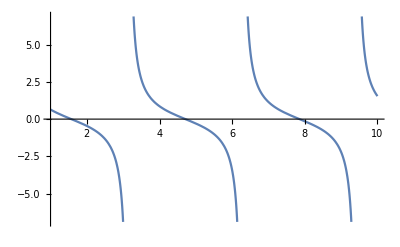

```mathematica
Plot[Cot[t],{t,1,10}]
```

```mathematica
_______________________________________________________________
```

## First try (this does not work)!

```mathematica
g[t_,x_] :=a[t]+b[t] (1-Cos[x]);
```

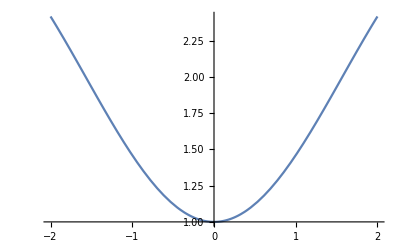

```mathematica
Plot[g[t,x]/.{a[t]->1,b[t]->1},{x,-2,2}]
```

```mathematica
PDE=D[u[t,x],t,t]-A D[u[t,x],x,x]- B (D[u[t,x],x])^2;
```

```mathematica
ODEs = Block[{u},u[t_,x_]:=g[t,x];PDE]
```

-A b[t] Cos[x]-B b[t]^2 Sin[x]^2+a''[t]+(1-Cos[x]) b''[t]

```mathematica
ODEs/.x->0/.A->0
```

a''[t]